The quantum Fourier transform (QFT) is a quantum analog of the classical discrete Fourier transform (DFT) and is a key component in many quantum algorithms, including Shor's algorithm. QFT circuits transform a quantum state from the computational basis to the Fourier basis.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Use QuantumCircuitOperator to create the corresponding quantum Fourier transform circuit of 3-qubits:

```mathematica
qft=QuantumCircuitOperator[{"Fourier",3}]
```

QuantumCircuitOperator[…]

Circuit diagram:

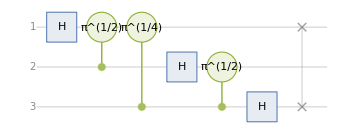

```mathematica
qft["Diagram"]
```

The matrix representation of the Fourier transform on three qubits:

```mathematica
qft["Matrix"]//MatrixForm
```

(1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2) | 1/(2 √2)
1/(2 √2) | ⅇ^((ⅈ π)/4)/(2 √2) | ⅈ/(2 √2) | (ⅈ ⅇ^((ⅈ π)/4))/(2 √2) | -1/(2 √2) | -ⅇ^((ⅈ π)/4)/(2 √2) | -ⅈ/(2 √2) | -(ⅈ ⅇ^((ⅈ π)/4))/(2 √2)
1/(2 √2) | ⅈ/(2 √2) | -1/(2 √2) | -ⅈ/(2 √2) | 1/(2 √2) | ⅈ/(2 √2) | -1/(2 √2) | -ⅈ/(2 √2)
1/(2 √2) | (ⅈ ⅇ^((ⅈ π)/4))/(2 √2) | -ⅈ/(2 √2) | ⅇ^((ⅈ π)/4)/(2 √2) | -1/(2 √2) | -(ⅈ ⅇ^((ⅈ π)/4))/(2 √2) | ⅈ/(2 √2) | -ⅇ^((ⅈ π)/4)/(2 √2)
1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2) | 1/(2 √2) | -1/(2 √2)
1/(2 √2) | -ⅇ^((ⅈ π)/4)/(2 √2) | ⅈ/(2 √2) | -(ⅈ ⅇ^((ⅈ π)/4))/(2 √2) | -1/(2 √2) | ⅇ^((ⅈ π)/4)/(2 √2) | -ⅈ/(2 √2) | (ⅈ ⅇ^((ⅈ π)/4))/(2 √2)
1/(2 √2) | -ⅈ/(2 √2) | -1/(2 √2) | ⅈ/(2 √2) | 1/(2 √2) | -ⅈ/(2 √2) | -1/(2 √2) | ⅈ/(2 √2)
1/(2 √2) | -(ⅈ ⅇ^((ⅈ π)/4))/(2 √2) | -ⅈ/(2 √2) | -ⅇ^((ⅈ π)/4)/(2 √2) | -1/(2 √2) | (ⅈ ⅇ^((ⅈ π)/4))/(2 √2) | ⅈ/(2 √2) | ⅇ^((ⅈ π)/4)/(2 √2))